Integral Calculus

Indefinite Integral (Anti-derivative)

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

Note: Mathematica does not include the arbitrary of integration.

Definite Integral

```mathematica
Integrate[Sin[x],{x,Pi/6,Pi/2}]
```

(√3)/2

Approximate value of a definite Integral

```mathematica
NIntegrate[Log[x]Exp[-x^2],{x,0,∞}]
```

-0.870058

NIntegrate is faster than other methods:

```mathematica
NIntegrate[Log[x]Exp[-x^2],{x,0,∞}]//Timing
Integrate[Log[x]Exp[-x^2],{x,0,∞}]//N//Timing
Integrate[Log[x]Exp[-x^2],{x,0,∞}]//Timing
```

{0.,-0.870058}

{2.46875,-0.870058}

{2.42188,-1/4 √π (EulerGamma+Log[4])}

Common unexpected output and what to do

```mathematica
Integrate[(16(x-1)^2)/(x^2-4)^2,{x,0,1}]
```

2-3 ArcTanh[1/2]

```mathematica
TrigToExp[2-3 ArcTanh[1/2]]
```

2-3/2 Log[3/2]-(3 Log[2])/2

```mathematica
Simplify[2-3/2 Log[3/2]-(3 Log[2])/2]
```

2-Log[27]/2

```mathematica
PowerExpand[2-Log[27]/2]
```

2-(3 Log[3])/2

Variable Integral Terminals

```mathematica
D[Integrate[t^2,{t,1,1/x}],x]
```

-1/x^4

Solving For An Unknown Integral Terminal

Example 1: The integral of 2/3(x^2-1)^(3/2) from x=2 to x=a where a>2 is 4. Find the value of a correct to three decimal places.

Option 1 (can take a long time and may give errors if the function has vertical asymptotes or some other type of discontinuity):

```mathematica
Solve[Integrate[2/3(x^2-1)^(3/2),{x,2,a}]==4,a]//N
```

$Aborted

Option 2: Use the Assuming and Solve commands (use Assuming to tell Mathematica of any restrictions on the unknown terminal).

```mathematica
Assuming[a>2,Solve[Integrate[2/3(x^2-1)^(3/2),{x,2,a}]==4,a,Reals]]//N
```

{{a→2.63833}}

Note: NIntegrate cannot be used when the unknown is in the terminal:

```mathematica
Solve[NIntegrate[2/3(x^2-1)^(3/2),{x,2,a}]==4,a,Reals]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[NIntegrate[2/3 (x^2-1)^(3/2),{x,2,a}]==4,a,ℝ]

The Assuming is a very useful command to know. Its use can be necessary when an unknown is in an integral terminal. It can also lead to simplifications that otherwise wouldn’t happen.
Example: Solve ∫_(1/2)^a 1/Log[x]ⅆx=-1/2 for a.

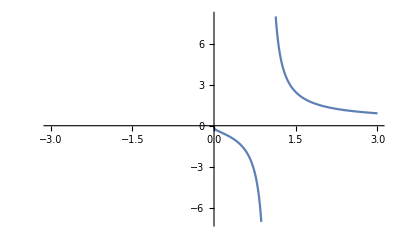

```mathematica
Plot[1/Log[x],{x,-3,3}]
```

```mathematica
Solve[Integrate[1/Log[x],{x,1/2,a}]==-1/2,a]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ConditionalExpression[-LogIntegral[1/2]+LogIntegral[a]==-1/2, Re[a]>0||a∉ℝ],a]

```mathematica
Assuming[a>0,Solve[Integrate[1/Log[x],{x,1/2,a}]==-1/2,a]]//N
```

{{a→0.732566}}

Area Bounded by a Curve and the x-axis

Example 2:
Find the area of the shaded region
-Graphics-

```mathematica
NIntegrate[RealAbs[Log[(x-1)^2]],{x,1.3,3}]
```

1.45021

Check:

```mathematica
-NIntegrate[Log[(x-1)^2],{x,1.3,2}]+NIntegrate[Log[(x-1)^2],{x,2,3}]
```

1.45021

Warning: Do NOT use

```mathematica
Abs[NIntegrate[Log[(x-1)^2],{x,1.3,3}]]
```

0.0949724

Trapezium Rule

-Graphics-
where the interval of integration is [a=x_0, b=x_n] and the number of trapezia is n.

Definitions:

```mathematica
ClearAll[x,n,a,b,h]
f[x_]:=1/(x+1)             (* The function f(x) *)
n:=4                    (* Number of trapezia is given *)
a:=0                    (* Value of a, that is, value of Subscript[x, 0] *)
b:=4                    (* Value of b, that is, Subscript[x, n] *)
h:=(b-a)/n              (* Step size (that is, width of each trapezium) *)

(* Note: n = (b - a)/h = (Subscript[x, n] - Subscript[x, 0])/h. Use this if the width of trapezia rather than the number of trapezia is given. *)
```

Algorithm:

```mathematica
(h/2)*(f[a]+2*Sum[f[a+i*h],{i,1,n-1}]+f[b])     (*Subscript[x, i]:=a+i*h*)
```

101/60

Area Bounded by a Curve and the x-axis

Example 3:
Find the area of the shaded region
-Graphics-

```mathematica
Integrate[Abs[Cos[x]-Sin[2x]],{x,0,Pi/2}]
```

1/2

Check:

```mathematica
Integrate[Cos[x]-Sin[2x],{x,0,Pi/6}]+Integrate[Sin[2x]-Cos[x],{x,Pi/6,Pi/2}]
```

1/2

Warning: Do NOT use

```mathematica
Abs[Integrate[Cos[x]-Sin[2x],{x,0,Pi/2}]]
```

0

Basic Properties - Common Question Types

Example 2 from SUP:
-Graphics-
Try finding and using a simple rule for f(x). Try f(x) = k where k is a constant:

```mathematica
Solve[Integrate[k,{x,0,a}]==a,k]
```

{{k→1}}

f(x) = 1 therefore f(x/5)=1:

```mathematica
2*Integrate[1+3,{x,0,5*a}]
```

40 a

Example 1 from SUP:
-Graphics-
Try finding and using a simple rule for f(x). f(x) = k where k is a constant obviously does not work:

```mathematica
Solve[{Integrate[k,{x,1,4}]==4,Integrate[k,{x,2,4}]==-2},k]
```

{}

Try f(x) = ax + b (a linear is the next simplest rule after a constant):

```mathematica
Solve[{Integrate[a*x+b,{x,1,4}]==4,Integrate[a*x+b,{x,2,4}]==-2},{a,b}]
```

{{a→-14/3,b→13}}

Therefore f(x)=-14/3x+13:

```mathematica
Integrate[-14x/3+13+x,{x,1,2}]
```

15/2